Genez, Inc.
9617 Black Watch Court
Charlotte, NC 28277

March 6, 2021

To: Chief Scientist, Vertextin Inc.
From: Aakriti Lakshmanan
Subj: Case Study: QSAR Study of an Antiadrenergic Amine

## Summary and Introduction

### Abstract:

As requested in the Scope of Work of March 4, 2021, we evaluated a dataset of 22 substitutions of the lead drug that contains the log(1/C), the Lipophilicity constant π, and the Hammett Constant, the Taft’s Steric Parameter and the logP values for each of the compounds.

### Introduction/Background Information:

In the following technical memo, we will primarily be examining a dataset of 22 substitutions of the lead drug, dimethylbromophenethylamine. The lead compound has a similar structure to compounds in the family of antiadrenergic drugs such as Norepinephrine. Anti-adrenergic drugs work by inhibiting the processes of the sympathetic nervous system. Beta receptors are receptors located in various parts of the body that are activated by a set of neurotransmitters known as catecholamines. Neurotransmitters that fall under the category of catecholamines include norepinephrine, epinephrine and dopamine. These neurotransmitters increase blood pressure and heart rate when the body undergoes a fight-or-flight response. [1] 

While this can be helpful in cases of danger or when the body needs to be alert, some people have an imbalance in the natural amounts of catecholamines within their body. This can lead to chronically increased blood pressure and heart rate, which can negatively affect heart health and can lead to heart failure. Therefore, antiadrenergics work by inhibiting the beta receptors for catecholamines in the body. When these drugs bind to the receptor before the neurotransmitters, the receptor is not activated and therefore the patient does not experience any fight-or-flight symptoms. [2]

Developed these drugs usually follows a specific process. After a lead drug has been established, researchers will try different substituents, including specific elements or functional groups, to see how they can change the function or qualities of the drug to make it better suited for a specific use within the body. Using these parameters and a set of experimental values, regression or statistical models can built and be used to predict the performance of novel parameter combinations. This process is more formally known as QSAR. [3] 

In the following tech memo, three specific parameters will be used to build a QSAR model for the lead drug. These parameters are the Lipophilicity constant, the Hammett Constant, the Taft’s Steric Parameter. Each of these parameters examine a different property of the compound: the Lipophilicity constant measures how well a compound can pass through lipid membranes, the Hammett Constant measures how likely a compound is to ionize, and Taft’s Steric Parameter measures steric hindrance, which is how much a specific substituent changes the shape of the overall molecule. Each of these parameters has their own effect on the drug, making it either less or more effective at inducing the biological activity it was designed for. 

These parameters will be used to predict the log(1/C). When a drug is used within the body, researchers can calculate the smallest concentration of the drug needed to be effective and have the directed biological activity. The way that this concentration is measured is standardized throughout the study to ensure optimal results. The concentration is then transformed into log(1/C), which also standardizes the value and allows for direct comparison between different combinations of substituents.

## Methodology

For this study, the list of 22 substitutions of the lead drug was collected from the NCSSM Canvas website. The following analyses were conducted:

Drug data was imported into Mathematica

Data was summarized through descriptive statistics

A multiple regression analysis was performed

The optimal Hammett Constant value was calculated

### Data Import and Description:

```mathematica
aaDrug = Import["/Users/aakritilakshmanan/Downloads/datalab1week4.csv"];
viableDrug=aaDrug;
aaDrug // TableForm
```

X | Y | Log 1/C Observed | Lipophilicity constant π | Hammett Constant | Taft's Steric Parameter | logP
H | H | 7.46 | 0. | 0. | 1.24 | 1.87
H | F | 8.16 | 0.15 | -0.07 | 1.24 | 2.41
H | Cl | 8.68 | 0.7 | 0.11 | 1.24 | 1.68
H | Br | 8.89 | 1.02 | 0.15 | 1.24 | 2.2
H | I | 9.25 | 1.26 | 0.14 | 1.24 | -0.14
H | Me | 9.3 | 0.52 | -0.31 | 1.24 | 2.2
F | H | 7.52 | 0.13 | 0.35 | 0.78 | 2.33
Cl | H | 8.16 | 0.76 | 0.4 | 0.27 | 1.64
Br | H | 8.3 | 0.94 | 0.41 | 0.08 | 2.17
I | H | 8.4 | 1.15 | 0.36 | -0.16 | -0.17
Me | H | 8.46 | 0.51 | -0.07 | 0. | 2.17
Cl | F | 8.19 | 0.91 | 0.33 | 0.27 | 2.06
Br | F | 8.57 | 1.09 | 0.34 | 0.08 | 2.76
Me | F | 8.82 | 0.66 | -0.14 | 0. | 2.62
Cl | Cl | 8.89 | 1.46 | 0.51 | 0.27 | 2.79
Br | Cl | 8.92 | 1.64 | 0.52 | 0.08 | 2.05
Me | Cl | 8.96 | 1.21 | 0.04 | 0. | 2.21
Cl | Br | 9. | 1.78 | 0.55 | 0.27 | 2.05
Br | Br | 9.35 | 1.96 | 0.56 | 0.08 | 2.78
Me | Br | 9.22 | 1.53 | 0.08 | 0. | 2.78
Me | Me | 9.3 | 1.03 | -0.38 | 0. | 2.85
Br | Me | 9.52 | 1.46 | 0.1 | 0.08 | 2.78

## Results

### Descriptive Statistics

We determined the mean, median, standard deviation, and quartiles for specific parameters within our data set, and produced a box/whisker plot for each of the variables. As seen in these plots, Taft’s Steric Parameter has the highest range of values when compared to the other parameters. The “standard” range for Taft’s Steric Parameter, which is defined as between the 1st and 3rd quartiles, would be between 0 and 1.24, as shown in the “Quartiles” row in the table below. Therefore, it would be acceptable for further substitutions of the lead drug to have steric parameters within this range.

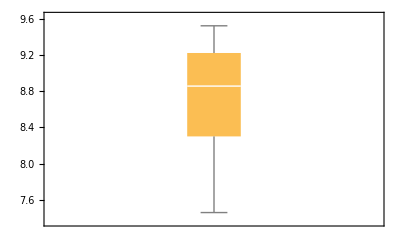
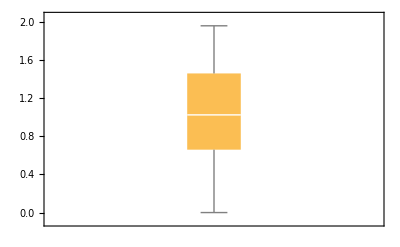
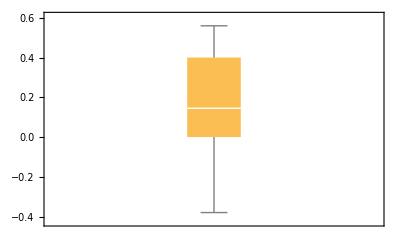
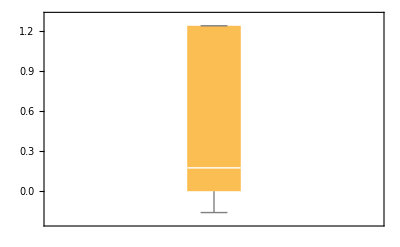
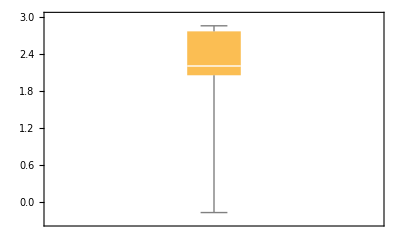
| Log 1/C Observed | Lipophilicity constant π | Hammett Constant | Taft's Steric Parameter | logP
Mean | 8.69636 | 0.994091 | 0.180909 | 0.433636 | 2.095
Median | 8.855 | 1.025 | 0.145 | 0.175 | 2.2
Standard Deviation | 0.568134 | 0.535027 | 0.273721 | 0.536581 | 0.814749
Quartiles | {8.3,8.855,9.22} | {0.66,1.025,1.46} | {0.,0.145,0.4} | {0.,0.175,1.24} | {2.05,2.2,2.76}
BoxWhisker Plot | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
header = aaDrug[[1]];
aaDrug = Delete[aaDrug,1];
{x1, y1, log1c, lipo,hammett,taft,logP} = Transpose[aaDrug];
descriptiveStats = Grid[{{"", header[[3]], header[[4]], header[[5]], header[[6]], header[[7]]}, {"Mean", Mean[log1c], Mean[lipo], Mean[hammett], Mean[taft], Mean[logP]}, {"Median", Median[log1c], Median[lipo], Median[hammett], Median[taft], Median[logP]}, {"Standard Deviation", StandardDeviation[log1c], StandardDeviation[lipo], StandardDeviation[hammett], StandardDeviation[taft], StandardDeviation[logP]}, {"Quartiles", Quartiles[log1c], Quartiles[lipo], Quartiles[hammett], Quartiles[taft], Quartiles[logP]}, {"BoxWhisker Plot", BoxWhiskerChart[log1c], BoxWhiskerChart[lipo], BoxWhiskerChart[hammett], BoxWhiskerChart[taft], BoxWhiskerChart[logP]}}, Frame -> All]
```

### Regression Calculation

We have used a multiple regression model using the parameters above to estimate log (1/C). Specifically, the parameters used for this multiple regression model are the lipophilicity constant, the Hammett constant and Taft’s Steric Parameter.  The calculated regression formula is as follows:

```mathematica
parametersTogethers = Transpose[{lipo,hammett,taft,log1c}];
myFit = LinearModelFit[parametersTogethers, {lipoA,hammettA,taftA},{lipoA,hammettA,taftA} ]; 
Print["log(1/C) =", TraditionalForm[Normal[myFit]]]
```

log(1/C) =-1.45961 hammettA+1.25864 lipoA+0.207918 taftA+7.61906

We also calculated the R^2 value for this regression to see how well the model predicts the log (1/C) value. In medicinal chemistry, R^2 values must be above. 0.9 to be acceptable. The closer the R^2 is to 1, the more accurate the model.

```mathematica
Print["R Squared Value = ", myFit["RSquared"]]
```

R Squared Value = 0.920254

### Optimal Drug Design

Preliminary studies of the lead drug have shown that a lipophilicity of 1.15 would make sure that the drug can go through lipid membranes in order to travel to the target receptor. In addition, these studies have also shown that the drug must have no steric hindrance to be effective. The optimal log (1/C) value is also given at 10.25. Therefore, given these values, we can use the previously calculated regression model to find the Hammett constant value needed to create the environment for the optimal drug. By substituting in the values of 1.15 for the lipophilicity constant, 0 for Taft’s Steric Parameter, and 10.25 for log(1/C), we find the value for Hammett Constant to be as follows:

```mathematica
hammetValue = NSolve[{myFit[1.15,hammettAB,0]==10.25}, hammettAB];
hammetValue[[1]]
```

{hammettAB→-0.810836}

Since the Hammett Constant value is negative, we can conclude that the new, most optimal drug would need substituents that are electron-donor groups. Therefore, the lead drug would perform better if it dissociates into ions.

Genez very much appreciates the opportunity to conduct this work and hopes that the results are satisfactory. We look forward to a long working relationship with Vertextin, and wish your company success in its scientific ventures.

I certify that this work was completed by me on March 6, 2021.  All references and resources are cited.  Assistance was provided by NAME OF PERSON(S) (if any)
  Electronic signature: -Graphics-

References:

https://en.wikipedia.org/wiki/Catecholamine

https://en.wikipedia.org/wiki/Adrenergic_antagonist

https://en.wikipedia.org/wiki/Quantitative_structure–activity_relationship